D:\study\phd_research\main\horsefly\viz_aid

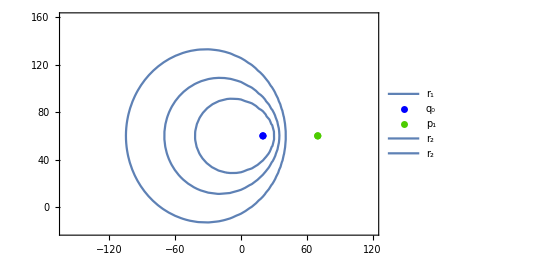

```mathematica
SetDirectory["D:\study\phd_research\main\horsefly\viz_aid"]
ClearAll["Global`*"]
q0 =Transpose@{{20},{60}};
p1 = Transpose@{{70},{60}};
plot1=ListPlot[q0, PlotStyle->Blue, PlotLegends->{Subscript[q,0]}];
plot2= ListPlot[p1, PlotStyle->{RGBColor[0.3,0.8,0]}, PlotLegends->{Subscript[p,1]}];
plot3= ContourPlot[
{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/14)Sqrt[(x-70)^2+(y-60)^2]==0},
{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,1]}];
plot4= ContourPlot[
{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/14)Sqrt[(x-70)^2+(y-60)^2]+1.8==0},
{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,2]}];
plot5= ContourPlot[
{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/14)Sqrt[(x-70)^2+(y-60)^2]+1==0},
{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,2]}];
s = Show[plot3, plot1,plot2,plot4 ,plot5, AspectRatio->Automatic]
s = Show[plot3, plot1,plot2,plot4,plot5,  AspectRatio->Automatic]
```

```mathematica
SetDirectory["D:\study\phd_research\main\horsefly\viz_aid"]
ClearAll["Global`*"]
q0 =Transpose@{{-30},{80}};
p1 = Transpose@{{-90},{30}};
v0  = 10;
v1 = 20;
plot1=ListPlot[q0, PlotStyle->Blue, PlotLegends->{Subscript[q,0]}];
plot2= ListPlot[p1, PlotStyle->{RGBColor[0.3,0.8,0]}, PlotLegends->{Subscript[p,1]}];
plot3= ContourPlot[
{(1/v0)  Sqrt[(x-q0[[1]][[1]])^2+(y-q0[[1]][[2]])^2]-(1/v1)Sqrt[(x-p1[[1]][[1]])^2+(y-p1[[1]][[2]])^2]==0},
{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,1]}];
plot4= ContourPlot[
{(1/v0)  Sqrt[(x-q0[[1]][[1]])^2+(y-q0[[1]][[2]])^2]-(1/v1)Sqrt[(x-p1[[1]][[1]])^2+(y-p1[[1]][[2]])^2]+1.2==0},
{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,2]}];
plot5= ContourPlot[
{(1/v0)  Sqrt[(x-q0[[1]][[1]])^2+(y-q0[[1]][[2]])^2]-(1/v1)Sqrt[(x-p1[[1]][[1]])^2+(y-p1[[1]][[2]])^2]+2.2==0},
{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,2]}];
s = Show[plot3, plot1,plot2,plot4,plot5,  AspectRatio->Automatic]
Export[Directory[] <> "\2drones_varied_t0.pdf",s]
```

```mathematica
SetDirectory["D:\study\phd_research\main\horsefly\viz_aid"]
ClearAll["Global`*"]
q0 =Transpose@{{10},{80}};
p1 = Transpose@{{-70},{30}};
qn = Transpose@{{10},{30}};
v0  = 10;
v1 = 20;
plot1=ListPlot[q0, PlotStyle->Blue, PlotLegends->{Subscript[q,0]}];
plot2= ListPlot[p1, PlotStyle->{RGBColor[0.3,0.8,0]}, PlotLegends->{Subscript[p,1]}];
plot3= ListPlot[qn, PlotStyle->Blue, PlotLegends->{Subscript[qn,1]}];
plot4= ContourPlot[
{(1/v0)  Sqrt[(x-q0[[1]][[1]])^2+(y-q0[[1]][[2]])^2]-(1/v1)Sqrt[(x-p1[[1]][[1]])^2+(y-p1[[1]][[2]])^2] + 2.7==0},
{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,1]}];
plot5 = ContourPlot[{Sqrt[(x-p1[[1]][[1]])^2 +(y-p1[[1]][[2]])^2] +  Sqrt[(x-qn[[1]][[1]])^2 +(y-qn[[1]][[2]])^2] == 100},{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,2]}, ContourStyle->{RGBColor[0.8,0.4,0]}];
plot6 = ContourPlot[{Sqrt[(x-p1[[1]][[1]])^2 +(y-p1[[1]][[2]])^2] +  Sqrt[(x-qn[[1]][[1]])^2 +(y-qn[[1]][[2]])^2] == 118},{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,2]}, ContourStyle->{RGBColor[0.8,0.4,0]}];
s = Show[plot4, plot5,plot6, plot1,plot2, plot3, AspectRatio->Automatic]
Export[Directory[] <> "\2drones_rendevouz_and_ellipse.pdf",s]
```

```mathematica
SetDirectory["D:\study\phd_research\main\horsefly\viz_aid"]
ClearAll["Global`*"]
q0 =Transpose@{{10},{80}};
p1 = Transpose@{{-70},{30}};
qn = Transpose@{{10},{30}};
v0  = 10;
v1 = 40;
plot1=ListPlot[q0, PlotStyle->Blue, PlotLegends->{Subscript[q,0]}];
plot2= ListPlot[p1, PlotStyle->{RGBColor[0.3,0.8,0]}, PlotLegends->{Subscript[p,1]}];
plot3= ListPlot[qn, PlotStyle->Blue, PlotLegends->{Subscript[qn,1]}];
plot4= ContourPlot[
{(1/v0)  Sqrt[(x-q0[[1]][[1]])^2+(y-q0[[1]][[2]])^2]-(1/v1)Sqrt[(x-p1[[1]][[1]])^2+(y-p1[[1]][[2]])^2]==0},
{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,1]},MaxRecursion->4];
plot6 = ContourPlot[{Sqrt[(x-p1[[1]][[1]])^2 +(y-p1[[1]][[2]])^2] +  Sqrt[(x-qn[[1]][[1]])^2 +(y-qn[[1]][[2]])^2] == 111.5},{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,2]}, ContourStyle->{RGBColor[0.8,0.4,0]}];
s = Show[plot4,plot6, plot1,plot2, plot3, AspectRatio->Automatic]
Export[Directory[] <> "\2drones_rendevouz_and_ellipse_1.pdf",s]
```

D:\study\phd_research\main\horsefly\viz_aid

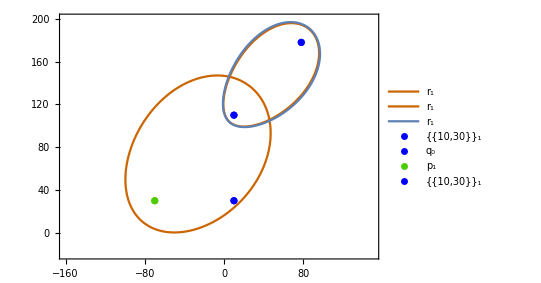

```mathematica
SetDirectory["D:\study\phd_research\main\horsefly\viz_aid"]
ClearAll["Global`*"]
q0 =Transpose@{{10},{110}};
p1 = Transpose@{{-70},{30}};
qn = Transpose@{{10},{30}};
p11 = Transpose@{{78},{178}};
v0  = 26;
v1 = 30;
plot1=ListPlot[q0, PlotStyle->Blue, PlotLegends->{Subscript[q,0]}];
plot2= ListPlot[p1, PlotStyle->{RGBColor[0.3,0.8,0]}, PlotLegends->{Subscript[p,1]}];
plot3= ListPlot[qn, PlotStyle->Blue, PlotLegends->{Subscript[qn,1]}];
plot4= ListPlot[p11, PlotStyle->Blue, PlotLegends->{Subscript[qn,1]}];
plot5= ContourPlot[
{(1/v0)  Sqrt[(x-q0[[1]][[1]])^2+(y-q0[[1]][[2]])^2]-(1/v1)Sqrt[(x-p1[[1]][[1]])^2+(y-p1[[1]][[2]])^2]+ 3.2==0},
{x,-160,150},{y,-20,200},PlotLegends->{Subscript[r,1]},MaxRecursion->4];
plot6= ContourPlot[
{(1/v0)  Sqrt[(x-q0[[1]][[1]])^2+(y-q0[[1]][[2]])^2]+(1/v1)Sqrt[(x-p1[[1]][[1]])^2+(y-p1[[1]][[2]])^2]==6},
{x,-160,150},{y,-20,200},PlotLegends->{Subscript[r,1]},MaxRecursion->4, ContourStyle->{RGBColor[0.8,0.4,0]}];
plot7= ContourPlot[
{(1/v1)  Sqrt[(x-q0[[1]][[1]])^2+(y-q0[[1]][[2]])^2]+(1/v0)Sqrt[(x-p11[[1]][[1]])^2+(y-p11[[1]][[2]])^2]==4.25},
{x,-160,150},{y,-20,200},PlotLegends->{Subscript[r,1]},MaxRecursion->4, ContourStyle->{RGBColor[0.8,0.4,0]}];
s = Show[plot7, plot6,plot5, plot4,plot1,plot2, plot3, AspectRatio->Automatic]
```

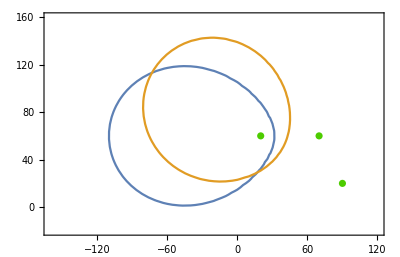

D:\study\phd_research\main\horsefly\viz_aid\3drones_left.pdf

```mathematica
ClearAll["Global`*"]
xx={20, 70, 90};SetDirectory["D:\study\phd_research\main\horsefly\viz_aid"]
ClearAll["Global`*"]
q0 =Transpose@{{10},{80}};
p1 = Transpose@{{-70},{30}};
qn = Transpose@{{10},{30}};
v0  = 10;
v1 = 40;
plot1=ListPlot[q0, PlotStyle->Blue, PlotLegends->{Subscript[q,0]}];
plot2= ListPlot[p1, PlotStyle->{RGBColor[0.3,0.8,0]}, PlotLegends->{Subscript[p,1]}];
plot3= ListPlot[qn, PlotStyle->Blue, PlotLegends->{Subscript[qn,1]}];
plot4= ContourPlot[
{(1/v0)  Sqrt[(x-q0[[1]][[1]])^2+(y-q0[[1]][[2]])^2]-(1/v1)Sqrt[(x-p1[[1]][[1]])^2+(y-p1[[1]][[2]])^2]==0},
{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,1]},MaxRecursion->4];
plot6 = ContourPlot[{Sqrt[(x-p1[[1]][[1]])^2 +(y-p1[[1]][[2]])^2] +  Sqrt[(x-qn[[1]][[1]])^2 +(y-qn[[1]][[2]])^2] == 111.5},{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,2]}, ContourStyle->{RGBColor[0.8,0.4,0]}];
s = Show[plot4,plot6, plot1,plot2, plot3, AspectRatio->Automatic]
Export[Directory[] <> "\2drones_rendevouz_and_ellipse_1.pdf",s]
yy ={60,60,20};SetDirectory["D:\study\phd_research\main\horsefly\viz_aid"]
ClearAll["Global`*"]
q0 =Transpose@{{20},{60}};
p1 = Transpose@{{70},{60}};
plot1=ListPlot[q0, PlotStyle->Blue, PlotLegends->{Subscript[q,0]}];
plot2= ListPlot[p1, PlotStyle->{RGBColor[0.3,0.8,0]}, PlotLegends->{Subscript[p,1]}];
plot3= ContourPlot[
{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/14)Sqrt[(x-70)^2+(y-60)^2]==0},
{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,1]}];
plot4= ContourPlot[
{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/14)Sqrt[(x-70)^2+(y-60)^2]+1.8==0},
{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,2]}];
plot5= ContourPlot[
{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/14)Sqrt[(x-70)^2+(y-60)^2]+1==0},
{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,2]}];
s = Show[plot3, plot1,plot2,plot4 ,plot5, AspectRatio->Automatic]
s = Show[plot3, plot1,plot2,plot4,plot5,  AspectRatio->Automatic]
data=Transpose@{xx,yy};
plot1= ListPlot[data, PlotStyle->{RGBColor[0.3,0.8,0]}];
plot2= ContourPlot[
{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/12)Sqrt[(x-70)^2+(y-60)^2]+2.8==0, (1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/15)Sqrt[(x-90)^2+(y-20)^2]+1.8==0},
{x,-160,120},{y,-20,160}];
s = Show[{plot2, plot1}, AspectRatio->Automatic]
Export[Directory[] <> "\3drones_left.pdf",s]
```

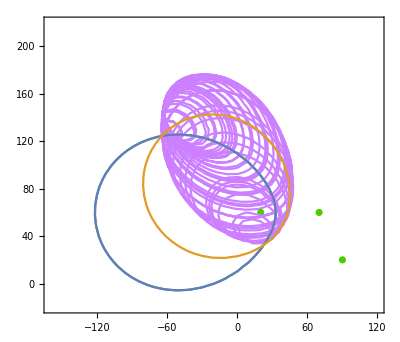

C:\Users\kienn\OneDrive\Documents\3drones_right.pdf

```mathematica
ClearAll["Global`*"]
xx={20, 70, 90};
yy ={60,60,20};
v0 = 10;
v1 = 12;
v2=  15;
data=Transpose@{xx,yy};
plot1= ListPlot[data, PlotStyle->{RGBColor[0.3,0.8,0]}];
plot2 = ContourPlot[(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/12)Sqrt[(x-70)^2+(y-60)^2]+1.8==0,{x,-160,120},{y,-20,220}];
plot3= ContourPlot[
{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/12)Sqrt[(x-70)^2+(y-60)^2]+1.8==0, (1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/15)Sqrt[(x-90)^2+(y-20)^2]+1.8==0},
{x,-160,120},{y,-20,220}];
points=Cases[Normal@plot2,Line[pts_]->pts,Infinity];
Join@@points;(*if you don't want disjoint components to be separate*)
points = points[[1]];
t0 = 1.8;

(*xq = 31.79870818081344;
yq = 51.87059811623722;
Print[(1/v1)Sqrt[(xq-70)^2+(yq-60)^2]];
ploti = ContourPlot[
(1/v1)Sqrt[(xq-70)^2+(yq-60)^2]+
(1/v1)*Sqrt[(x-xq)^2+(y-yq)^2]-
(1/v2)*Sqrt[(x-90)^2+(y-20)^2]
==0,
{x,-160,160},{y,-40,160}];
s = Show[ploti, AspectRatio->Automatic]
*)

plotList = {};
Do[
xq = i[[1]];
yq= i[[2]];
ploti=ContourPlot[
(1/v1)Sqrt[(xq-70)^2+(yq-60)^2]+
(1/v1)Sqrt[(x-xq)^2+(y-yq)^2]-
(1/v2)Sqrt[(x-90)^2+(y-20)^2]
==0,
{x,-160,120},{y,-20,220}, ContourStyle->RGBColor[0.8,0.5,1]];
AppendTo[plotList,ploti];
,{i, points}]
PrependTo[plotList,plot1];
PrependTo[plotList,plot2];
AppendTo[plotList,plot3];
s = Show[plotList, AspectRatio->Automatic]
Export[Directory[] <> "\3drones_center.pdf",s]
```

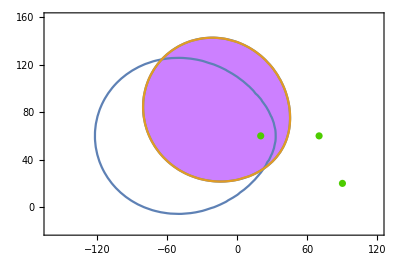

C:\Users\kienn\OneDrive\Documents\3drones_right.pdf

```mathematica
ClearAll["Global`*"]
xx={20, 70, 90};
yy ={60,60,20};
data=Transpose@{xx,yy};
plot1= ListPlot[data, PlotStyle->{RGBColor[0.3,0.8,0]}];
plot2= ContourPlot[
{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/12)Sqrt[(x-70)^2+(y-60)^2]+1.8==0, (1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/15)Sqrt[(x-90)^2+(y-20)^2]+1.8==0},
{x,-160,120},{y,-20,160}];
plot3= RegionPlot[
{ (1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/15)Sqrt[(x-90)^2+(y-20)^2]+1.8<0},
{x,-160,120},{y,-20,160}, PlotStyle->RGBColor[0.8,0.5,1]];
s = Show[{plot3, plot2, plot1}, AspectRatio->Automatic]
Export[Directory[] <> "\3drones_right.pdf",s]
```

```mathematica
Show[List,AspectRatio->Automatic]
```

Show::gtype: Symbol is not a type of graphics.

```mathematica
Show[List,AspectRatio->Automatic]
```

Show::gtype: Symbol is not a type of graphics.

Show[List,AspectRatio→Automatic]

```mathematica
Plot3D[{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/12)Sqrt[(x-70)^2+(y-60)^2]+1.8, z=8},{x,-300,300},{y,-300,300},ColorFunction->"RustTones"]
```

-Graphics3D-

D:\study\phd_research\main\horsefly\viz_aid

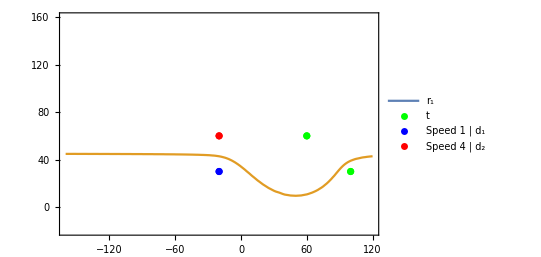

D:\study\phd_research\main\horsefly\viz_aid\2drones_2pairs.pdf

30

```mathematica
SetDirectory["D:\study\phd_research\main\horsefly\viz_aid"]
ClearAll["Global`*"];
t1 = Transpose@{{60},{60}};
t2 = Transpose@{{100},{30}};
d1 =Transpose@{{-20},{30}};
d2 = Transpose@{{-20},{60}};
plot1=ListPlot[d1, PlotStyle->Blue, PlotLegends->{Subscript[d,1]"Speed 1 |"}];
plot2= ListPlot[d2, PlotStyle->Red,PlotLegends->{Subscript[d,2]"Speed 4 |"}]; 
plot3 = ListPlot[t1, PlotStyle->Green, PlotLegends->{"t"}]; 
plot4 = ListPlot[t2, PlotStyle->Green]; 
v :=1.5;
plot5= ContourPlot[
{ {Sqrt[(x-d1[[1,1]])^2+(y-d1[[1,2]])^2]+Sqrt[(x-t2[[1,1]])^2+(y-t2[[1,2]])^2]== (Sqrt[(x+20)^2+(y-60)^2]/v+Sqrt[(x-100)^2+(y-30)^2]/v),Sqrt[(x-d1[[1,1]])^2+(y-d1[[1,2]])^2]-Sqrt[(x-60)^2+(y-60)^2]== (Sqrt[(x+20)^2+(y-60)^2]/v-Sqrt[(x-100)^2+(y-30)^2]/v)}},
{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,1]}];
s = Show[plot5,plot3,plot1,plot2,plot4,AspectRatio->Automatic]
Export[Directory[] <> "\2drones_2pairs.pdf",s]
d1[[1,2]]
```

```mathematica
points=Cases[Normal@plot5,Line[pts_]->pts,Infinity];
Join@@points;(*if you don't want disjoint components to be separate*)
points
```

{}

```mathematica
Reduce[{0<x<L,Sqrt[(x-lx)^2+(z-ly)^2]/a+Sqrt[(x-ex)^2+(z-ey)^2]/b<C},z]
```

$Aborted

```mathematica
RegionPlot[{ Sqrt[(x-10)^2+(y-20)^2]+ Sqrt[(x-50)^2+y^2]<105},
{x,-160,120},{y,-20,160}, PlotStyle->RGBColor[0.8,0.5,1]];
```

```mathematica
Plot3D[Sqrt[(x-10)^2+(y-20)^2]+ Sqrt[(x-50)^2+y^2],{x,-1000,1000},{y,-1000,1000}]
```

-Graphics3D-

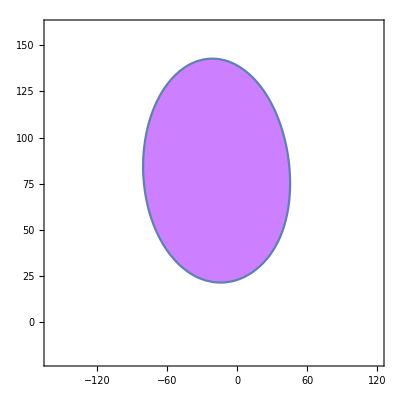

```mathematica
%2
```